# Asymptotics of the weight 11 Euler characteristic

This Notebook is part of the supplementary material of our paper “Moduli spaces of curves with polynomial point counts”.
It contains auxiliary computations that are used in section 6. The individual computations are referenced in the main text by the section titles (IDs) below.

## CKASYMP - Asymptotic behavior of the constants

Our goal here is to compute  and  and show that  for g=100.

```mathematica
CKAdelta[g_,k_,Gamma_]:=Sum[(2Pi)^J(J-1)!Zeta[2]/((J-Gamma-1)!Gamma!(J-k+1)!2^(g-k-J)),{J,Max[k,Gamma+1],g-k-1}]
CKAbeta[g_,k_,Gamma_]:=2^(k-2)Exp[2Pi](2Pi)^(g-k)/(Gamma!(g-2k-Gamma+1)!)
```

```mathematica
(** The sum of delta and beta should be <10^-14 **)
Table[CKAdelta[100,k,Gam]//N,{k,1,4},{Gam,0,10}]
Table[CKAbeta[100,k,Gam]//N,{k,1,4},{Gam,0,10}]
```

{{7.44188×10^-25,8.60759×10^-24,5.01514×10^-23,1.95978×10^-22,5.77259×10^-22,1.3661×10^-21,2.70406×10^-21,4.60267×10^-21,6.87471×10^-21,9.15073×10^-21,1.09874×10^-20},{1.87035×10^-23,2.35036×10^-22,1.47677×10^-21,6.18589×10^-21,1.94336×10^-20,4.88419×10^-20,1.02294×10^-19,1.83638×10^-19,2.88458×10^-19,4.02763×10^-19,5.06127×10^-19},{4.7007×10^-22,6.37716×10^-21,4.30225×10^-20,1.92584×10^-19,6.43887×10^-19,1.71595×10^-18,3.79846×10^-18,7.18626×10^-18,1.18651×10^-17,1.73723×10^-17,2.28429×10^-17},{1.18141×10^-20,1.7209×10^-19,1.24155×10^-18,5.92143×10^-18,2.10228×10^-17,5.93091×10^-17,1.38592×10^-16,2.76076×10^-16,4.78812×10^-16,7.34815×10^-16,1.01072×10^-15}}

{{3.0028×10^-75,2.97277×10^-73,1.45666×10^-71,4.70986×10^-70,1.13037×10^-68,2.1477×10^-67,3.36472×10^-66,4.47027×10^-65,5.14081×10^-64,5.19794×10^-63,4.67814×10^-62},{9.27337×10^-72,8.99517×10^-70,4.31768×10^-68,1.36727×10^-66,3.21307×10^-65,5.97632×10^-64,9.16368×10^-63,1.19128×10^-61,1.34019×10^-60,1.3253×10^-59,1.16626×10^-58},{2.74872×10^-68,2.61128×10^-66,1.2273×10^-64,3.80464×10^-63,8.75067×10^-62,1.59262×10^-60,2.38893×10^-59,3.03736×10^-58,3.34109×10^-57,3.22973×10^-56,2.77756×10^-55},{7.81326×10^-65,7.26633×10^-63,3.34251×10^-61,1.0139×10^-59,2.28126×10^-58,4.06065×10^-57,5.95562×10^-56,7.40198×10^-55,7.95713×10^-54,7.51507×10^-53,6.31266×10^-52}}

```mathematica
(*************)
```

## CKASYMP2- Asymptotic behavior of the constants

Our goal here is to compute  and  and show that  for g=100.

```mathematica
CKA2deltaprime[g_,k_,Gamma_]:=Sum[(2Pi)^J(J-1)!Zeta[2]/((J-Gamma-1)!Gamma!(J-k)!2^(g-k-J)),{J,Max[k+1,Gamma+1],g-k-1}]
CKA2betaprime[g_,k_,Gamma_]:=2^(k-1)Exp[2Pi](2Pi)^(g-k)/(Gamma!(g-2k-Gamma)!)
```

```mathematica
(** The sum of deltaprime and betaprime should be <10^-13 **)
Table[CKA2deltaprime[100,k,Gam]//N,{k,1,4},{Gam,0,10}]
Table[CKA2betaprime[100,k,Gam]//N,{k,1,4},{Gam,0,10}]
```

{{9.35175×10^-24,1.17518×10^-22,7.38387×10^-22,3.09295×10^-21,9.71678×10^-21,2.44209×10^-20,5.11471×10^-20,9.1819×10^-20,1.44229×10^-19,2.01382×10^-19,2.53064×10^-19},{2.35035×10^-22,3.18858×10^-21,2.15112×10^-20,9.62919×10^-20,3.21944×10^-19,8.57974×10^-19,1.89923×10^-18,3.59313×10^-18,5.93253×10^-18,8.68614×10^-18,1.14215×10^-17},{5.90707×10^-21,8.60449×10^-20,6.20774×10^-19,2.96072×10^-18,1.05114×10^-17,2.96546×10^-17,6.92961×10^-17,1.38038×10^-16,2.39406×10^-16,3.67407×10^-16,5.05359×10^-16},{1.48461×10^-19,2.311×10^-18,1.77643×10^-17,9.00127×10^-17,3.38591×10^-16,1.00948×10^-15,2.4869×10^-15,5.21088×10^-15,9.48621×10^-15,1.52509×10^-14,2.1935×10^-14}}

{{5.94554×10^-73,5.82663×10^-71,2.82591×10^-69,9.04293×10^-68,2.1477×10^-66,4.03767×10^-65,6.25838×10^-64,8.2253×10^-63,9.35628×10^-62,9.35628×10^-61,8.32709×10^-60},{1.79903×10^-69,1.72707×10^-67,8.20359×10^-66,2.57046×10^-64,5.97632×10^-63,1.09964×10^-61,1.66779×10^-60,2.1443×10^-59,2.38554×10^-58,2.33252×10^-57,2.0293×10^-56},{5.22257×10^-66,4.90921×10^-64,2.28278×10^-62,7.00054×10^-61,1.59262×10^-59,2.86672×10^-58,4.2523×10^-57,5.34575×10^-56,5.81351×10^-55,5.55513×10^-54,4.72186×10^-53},{1.45327×10^-62,1.337×10^-60,6.08337×10^-59,1.82501×10^-57,4.06065×10^-56,7.14674×10^-55,1.03628×10^-53,1.27314×10^-52,1.35271×10^-51,1.26253×10^-50,1.0479×10^-49}}

```mathematica
(*************)
```

## LAEVAL - Evaluation of the error terms and

Here we have to evaluate  and  for k=2,3,4.

```mathematica
LAEphi[x_,k_,Gamma_]:=Sum[x^j (j-1)!/(j-k+1)!/(j-Gamma-1)!/Gamma!,{j,Max[k,Gamma+1],Infinity}]
LAElambda[g_,k_,Gamma_]:=If[g>=2k,2^k Zeta[2]^(k-1)/(k-1)!/(2Pi)^(k-1)(Abs[LAEphi[2Pi ⅈ,k,Gamma]]+10^(-14))(g-2k)!/(g-2)!,0]
LAElambdaprime[g_,k_,Gamma_]:=If[g>=2k+1,2^k Zeta[2]^(k-1)/(k-2)!/(2Pi)^(k-1)(Abs[LAEphi[2Pi ⅈ,k+1,Gamma]]+10^(-13))(g-2k-1)!/(g-2)!,0]
```

```mathematica
Table[LAElambda[600,k,10],{k,2,4}]//N
Table[LAElambdaprime[600,k,10],{k,2,4}]//N
```

{0.000487044,4.24646×10^-9,2.41299×10^-14}

{9.65108×10^-6,1.63969×10^-10,1.37324×10^-15}

```mathematica
(***********)
```

## DELTAEVAL - Evaluation of the error terms and

```mathematica
DELphi[x_]:=Sum[x^J/J/10!/(J-11)!,{J,11,Infinity}]
DELphi[x_,Gamma_]:=Sum[x^J/J/Gamma!/(J-Gamma-1)!,{J,Gamma+1,Infinity}]
DELDelta[g_, kmin_]:=Sum[(31/10)^(k-1)(2Zeta[2])^k DELphi[2Pi k]/ (2Pi)^{k-1}/ k!(g-2k)!/(g-2)!,{k,kmin, (g-1)/2}]
DELDelta[g_, kmin_,Gamma_]:=Sum[(31/10)^(k-1)(2Zeta[2])^k DELphi[2Pi k,Gamma]/ (2Pi)^{k-1}/ k!(g-2k)!/(g-2)!,{k,kmin, (g-1)/2}]
DELAprimes={156/7,6999/70,9938/35,13771/21};
DELDeltaprime[g_,k_]:=1/k! DELAprimes[[k-1]](2Zeta[2])^k DELphi[2Pi k]/(2Pi)^(k-1) (g-2k-2)!/(g-2)!
DELDeltaprime[g_,k_,Gamma_]:=If[g-2k-2>=0,1/k! DELAprimes[[k-1]](2Zeta[2])^k DELphi[2Pi k,Gamma]/(2Pi)^(k-1) (g-2k-2)!/(g-2)!,0]
```

```mathematica
DELDelta[600,5]//N
```

General::munfl: 451302514611022222119906091571193923850834154614488607763201/(1248527941859620157537312514009253069015354201902810627891444551550597581240029«213»93715200000000000000000000000000000000000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 13990377952941688885717088838707011639375858793049146840659231/(1811424904140396534728975130354678941393853810952931964288466769364802690351700«225»52000000000000000000000000000000000000000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 433701716541192355457229753999917360820651622584523552060436161/(1315652254362410795114209690659635724191571862217297232883870579246469563239747«234»40000000000000000000000000000000000000000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.10478}

```mathematica
Table[DELDeltaprime[600,k],{k,2,4}]//N
```

{0.641878,0.0521099,0.000578797}

```mathematica
(***********)
```

## FKPRIME

Our goal here is to compute minimal  such that  for all  and k=2,3,4,5.
We do this by computing  for  in a large enough range. The necessary range of  needs to be computed to have a valid result.
Note we use memoization to compute the values of more efficiently.

```mathematica
(*maxn is the maximum allowed value of any summand *)
FKPFprime[n_,k_, maxn_]:=FKPFprime[n,k, maxn]=If [k==1, If[n<= maxn,n!,0], Sum[j!FF3p[n-j,k-1,maxn],{j,1,Min[n-k+1,maxn]}]]
FKPFprime[n_,k_]:=FKPFprime[n,k,n-k-1]
(* The error estimate from the proof. It is monotonically decreasing for n>2k *)
FKPerrterm[n_,k_]:=(Sum[k (n-k-1-q)! (31/10)^{k-2} (q+3)!,{q,1,k}]+Binomial[n-1,k-1](n-2k-2)!(k+5)!)/(n-k-1)!
FKPAprime[k_, maxn_]:=Max[Table[FKPFprime[n,k]/(n-k-1)!,{n,k,maxn}]]
```

```mathematica
(*Compute A's*)
Table[FKPAprime[k,50],{k,2,5}]
```

{156/7,6999/70,9938/35,13771/21}

Now we check that our range of N (up to 50) is actually large enough. This follows if the difference of the computed A_k’ to the asymptotic value is larger than our error estimate. Hence our above estimate for the A_k’ is rigorous if all the numbers of the following computation turn out positive.

```mathematica
FKPAprimeasymp[k_]:=6k(k−1)+2k(k−1)(k−2)
(* the numbers should all be positive for the computation to be valid *)
With[{maxn=50},Table[FKPAprime[k, maxn]-FKPAprimeasymp[k]- FKPerrterm[maxn,k]//N,{k,2,5}]]
```

{{6.61504},{34.4139},{95.131},{172.166}}

```mathematica
(***********)
```

## ATILDE

```mathematica
ATIrhs[g_] := Sum[Sum[LAElambda[g,k,Gam]+LAElambdaprime[g,k,Gam],{k,1,4}]+Sum[DELDeltaprime[g,k,Gam],{k,2,4}]+DELDelta[g,5,Gam],{Gam,0,10}]
```

```mathematica
Max[Table[ATIrhs[g],{g,1,150}]//N]
```

General::munfl: 328287884030704474260910865698590429953856653070549658688924765621538317155127527681/(5640093542210763743460259419760990507620221572848236147605305392518699033468379«233»00000000000000000000000000000000000000000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 328287884030704474260910865698590429953856653070549658688924765621538317155127527681/(1174571861488971751019025453766098340634560429139188226294946138886433830461986«234»00000000000000000000000000000000000000000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

4.29987×10^17

```mathematica
(***********)
```

## CLAMBDA

```mathematica
CLAratio[n_]:=Sum[(l/2)^(2Floor[n/l]-1)Floor[4 n/(3 l)]!,{l,2,Floor[n/2]}]/Floor[2n/3]!
```

```mathematica
(*This should stay below 2 *)
```

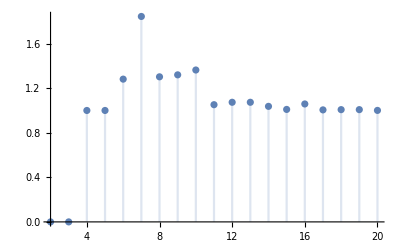

```mathematica
DiscretePlot[CLAratio[n],{n,2,20}]
```

```mathematica
(***********)
```

## ELAMBDA

2

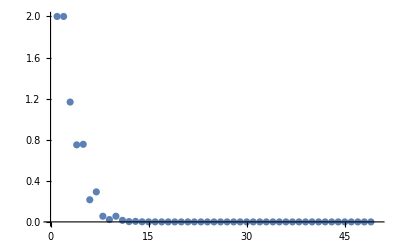

```mathematica
(*the first 49 terms of the series in the proof*)
(*the series has been computed by the python code*)
ELAseries=2*u+2*u^2+7/3*u^3+3/2*u^4+68/15*u^5+31/6*u^6+589/84*u^7+397/60*u^8+739/45*u^9+199/5*u^10+4979/66*u^11+4337/36*u^12+230645/1092*u^13+56453/140*u^14+142919/180*u^15+24043/16*u^16+32527/12*u^17+213872/45*u^18+42134889/5320*u^19+448452673/34650*u^20+8721719/420*u^21+130128748/3795*u^22+1086457063/16560*u^23+986595221/7800*u^24+6332438599/27300*u^25+1214854181/3276*u^26+196172651/378*u^27+215846021/210*u^28+1485958581/580*u^29+406279180163/61380*u^30+3908913785677/229152*u^31+3387036357919/85680*u^32+22308868674161/235620*u^33+390203329354/1785*u^34+1377911639089/2520*u^35+3202050445534/2223*u^36+261414581402939/67340*u^37+711260193886763/77805*u^38+1545902673240533/65520*u^39+129508545052269233/1894200*u^40+104533142753719007/568260*u^41+15469328444318459/32340*u^42+545268837520703/420*u^43+8673205191335728111/2390850*u^44+198917378999747083/18900*u^45+99532898565569887/3220*u^46+535097197161732869/6580*u^47+922543648716478065421/3898440*u^48+345666142040202195031/464100*u^49;
ELAseriescoeff=CoefficientList[ELAseries,u];
ELAratios = Table[ELAseriescoeff[[j+1]] /Floor[2j/3]!,{j,1,49}];
ELAmax=Max[ELAratios]
ListPlot[ELAratios,PlotRange-> {{0,50},{0,ELAmax}}]
```

```mathematica
(************)
```

## FLAMBDA

```mathematica
FLAa = 2
FLAE = 120
FLAFprime = Sum[(FLAa FLAE)^k/k!/(k-1)!,{k,1,Infinity}]
FLAF = 4 FLAFprime +1
FLAF//N
```

2

120

4 √15 BesselI[1,8 √15]

1+16 √15 BesselI[1,8 √15]

1.25397×10^14

```mathematica
(************)
```

## XEVAL

```mathematica
(*this uses the myZ70 series imported from the python code *)
```

```mathematica
XEVX1[g_,n0_]:=Sum[Sum[Abs[myZ70coeffW[[ n+1 ]][[11-Gam]]](g-n-2)!/(g-2)!(2Pi)^n Sum[LAElambda[g-n,k,Gam]+If[k>=2,LAElambdaprime[g-n,k,Gam],0],{k,1,4}],{n,1,n0}], {Gam,0,10}]

XEVX2[g_,n0_]:=Sum[Sum[Abs[myZ70coeffW[[ n+1 ]][[11-Gam]]](g-n-2)!/(g-2)!(2Pi)^n  (DELDelta[g-n,5,Gam] +Sum[DELDeltaprime[g,k,Gam],{k,2,4}] ),{n,1,n0}], {Gam,0,10}]
```

```mathematica
XEVX1[600,60]//N
```

0.790506

```mathematica
XEVX2[600,60]//N
```

General::munfl: 13990377952941688885717088838707011639375858793049146840659231/(4079432225620605823958523171082493702181458966244117227799141148076735943278834«216»44000000000000000000000000000000000000000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 433701716541192355457229753999917360820651622584523552060436161/(2303744798962341712469039205538194321883821695818593069587808363492898629221434«225»80000000000000000000000000000000000000000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 13444753212776963019174122373997438185440200300120230113873520991/(1316805783120161163860343008034716429945132424871054559580745898599014501911745«234»00000000000000000000000000000000000000000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.0148095}

```mathematica
(************)
```

## X3EVAL

```mathematica
X3Eeta[g_,n0_]:=Sum[(2n/3)!(g-n-2)!(2Pi)^(n+2)/(g-2)!,{n,n0,g-2}]
X3EF = 3.3 10^19
X3EAtilde=10^20
```

3.3×10^19

100000000000000000000

```mathematica
X3Eeta[600,60]//N
```

General::munfl: 1532495540865888858358347027150309183618739122183602176/(1805548862636106429266798026948261284620746616604642734224932928382236103649546«205»70441069000701414681555107371094744106466444593962508752458210632801055908203125) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 24519928653854221733733552434404946937899825954937634816/(3647549736344320994391744346208218578426726767004956534342183194751946788650391«208»63066924742007959585659087368574903464366054014816550114838098227977752685546875) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3064991081731777716716694054300618367237478244367204352/(5478320776635014626886362672373930379298798780749292608292309493983590874287733«209»07283271604682754823146554575797612886341772025496694706465490996837615966796875) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.55579×10^-68

```mathematica
X3EF *X3EAtilde *X3Eeta[600,60]//N
```

5.13411×10^-29

```mathematica
(************)
```

```mathematica
(*****Import from python code ****)
```

```mathematica
myZ70=(1-w+O(w^11))*u^2+(-1/12+13/12*w-w^3+O(w^11))*u^3+(-w+w^2+w^3-w^4+O(w^11))*u^4+(7/1440+779/720*w-601/288*w^2+11/12*w^3+13/12*w^4-w^6+O(w^11))*u^5+(7/1440-161/160*w+479/480*w^2+1/288*w^3-2*w^4+2*w^5+w^6-w^7+O(w^11))*u^6+(1549/362880+249407/120960*w-55913/17280*w^2+13541/51840*w^3+4313/1440*w^4-1177/288*w^5+23/12*w^6+13/12*w^7-w^9+O(w^11))*u^7+(667/181440-92107/45360*w+11743/3024*w^2-5177/3240*w^3-37067/25920*w^4+901/720*w^5-23/288*w^6-2*w^7+2*w^8+w^9-w^10+O(w^11))*u^8+(39503/12441600+46404997/21772800*w-64998739/14515200*w^2+7545557/4354560*w^3+76969741/17418240*w^4-8483/1440*w^5+60881/51840*w^6+4313/1440*w^7-1177/288*w^8+23/12*w^9+13/12*w^10+O(w^11))*u^9+(80281/29030400-29810213/29030400*w+7889981/1612800*w^2-92003533/14515200*w^3-24286327/5806080*w^4+849683/71680*w^5-52049/6480*w^6+68953/25920*w^7-539/720*w^8+265/288*w^9-2*w^10+O(w^11))*u^10+(3992873/1642291200+981466313/459841536*w-2397120139/522547200*w^2+3743093017/522547200*w^3-512030137/149299200*w^4-5145214993/1045094400*w^5+14610697/8709120*w^6+136925917/17418240*w^7-1277/160*w^8+9041/51840*w^9+5753/1440*w^10+O(w^11))*u^11+(885527/410572800-15621787/3942400*w+22219727/2534400*w^2-1363763447/261273600*w^3-312298517/43545600*w^4+682413041/29030400*w^5-2863527337/130636800*w^6-85040983/17418240*w^7+120901747/5806080*w^8-22181/1620*w^9+92713/25920*w^10+O(w^11))*u^12+(726510117493/376610217984000+137081836147121/62768369664000*w-93577449761119/9656672256000*w^2+16371045412933/1034643456000*w^3-380417324759/39414988800*w^4-98107191979/12541132800*w^5+1617660673669/75246796800*w^6-15200598149/1045094400*w^7-661259293/1045094400*w^8-7577903/8709120*w^9+202123357/17418240*w^10+O(w^11))*u^13+(130919833477/75322043596800-234286900677799/75322043596800*w+207536360450299/25107347865600*w^2-51870558807047/5794003353600*w^3-8556009248179/827714764800*w^4+1482028247503/55180984320*w^5-1244398517101/75246796800*w^6-549992284529/75246796800*w^7+545029411/18662400*w^8-1380073061/65318400*w^9-244061383/17418240*w^10+O(w^11))*u^14+(7124308550959/4519322615808000+14033341728743027/4519322615808000*w-25175689360044563/1506440871936000*w^2+151083690614607931/4519322615808000*w^3-56000365545280399/4519322615808000*w^4-4228198044429397/115880067072000*w^5+2333910076471399/49662885888000*w^6-62061115927361/9932577177600*w^7-77366174203/1672151040*w^8+5368549668589/75246796800*w^9-52020181649/1045094400*w^10+O(w^11))*u^15+(1083235265129/753220435968000-1455364816391/4828336128000*w+585025510926107/75322043596800*w^2-738889264209143/37661021798400*w^3+1769347396863857/75322043596800*w^4+2827023041325779/188305108992000*w^5-1069759916488927/14485008384000*w^6+32005912826257/413857382400*w^7-98981268718973/1655429529600*w^8+109650313009/2090188800*w^9-3270693889769/75246796800*w^10+O(w^11))*u^16+(48637601903531323/36877672544993280000+30403992071504321471/4609709068124160000*w-12774105402081605119/542318713896960000*w^2+6729558159372966373/271159356948480000*w^3+1544161526264610751/154948203970560000*w^4-2488091326482618331/54231871389696000*w^5+335980665083819801/21692748555878400*w^6+6245123627071611551/54231871389696000*w^7-7750684843192166501/33373459316736000*w^8+4691175750368507/24831442944000*w^9-15470629474865/397303087104*w^10+O(w^11))*u^17+(6402143044685083/5268238934999040000+292238485265496443/39023992111104000*w+12091717807061040899/614627875749888000*w^2-2797908860648659/34334834688000*w^3+5412128200129776557/72309161852928000*w^4+27235103590186361647/361545809264640000*w^5-10463785797868930777/36154580926464000*w^6+12950013879349454461/36154580926464000*w^7-2472206752754298799/13147120336896000*w^8-1332891563370637213/33373459316736000*w^9+147848065336553/1241572147200*w^10+O(w^11))*u^18+(595649911027648950103/529710888436283473920000+332197442807097204106709/58856765381809274880000*w+7665718130115170367937/774431123444858880000*w^2-2346166129905575836057/232329337033457664000*w^3-1195687072702666806727/44253207053991936000*w^4+128356415611048481309/1183240830320640000*w^5-4343611024616148518323/19523473700290560000*w^6+254581215986577841681/929689223823360000*w^7-268085613511972862509/1041251930682163200*w^8+1333579985119446404761/9371267376139468800*w^9+8400808882099863767/108463742779392000*w^10+O(w^11))*u^19+(69160600834636404073/66213861054535434240000-774220537377613908647171/132427722109070868480000*w+1187131213940408564037181/14714191345452318720000*w^2-343086394119542056029677/2323293370334576640000*w^3-1169135382851209271683/92931734813383065600*w^4+2097598698739272195391/5028773528862720000*w^5-6790889315258625405649/9761736850145280000*w^6+59510914281430196393/126775803248640000*w^7+75226529228202384239/1626956141690880000*w^8-3738379547670984211031/11714084220174336000*w^9+1140816184699127927489/11714084220174336000*w^10+O(w^11))*u^20+(763352895472413158287/784052896093175808000000-15334580747386307741504400079/349609186367947092787200000*w+7366392539015964687130299769/77690930303988242841600000*w^2+676812513442784269857769/11318608727271014400000*w^3-749448309407798196752717341/1513459681246524211200000*w^4+296368082290493759225726983/464658674066915328000000*w^5-1333538887526413549860511/10138007434187243520000*w^6-60627009428317185924487/159311545394370969600*w^7+19721941164962395566833/89250165487042560000*w^8+1498268471765467263686683/2811380212841840640000*w^9-7047705918080824224695417/5622760425683681280000*w^10+O(w^11))*u^21+(353646474533857102804133/388454651519941214208000000-155701812080559702658066681769/1165363954559823642624000000*w+26795536289775643977667296397/233072790911964728524800000*w^2+60893386987449676570066253869/233072790911964728524800000*w^3-663527045777317357507442729/963110706247788134400000*w^4+10754267198632570479759751891/17657029614542782464000000*w^5+4543674672752003019906487/71485949856448512000000*w^6-1444566888129261774049987/2478179595023548416000*w^7+5172377259551998106597/19704581990645760000*w^8+35114429596423874724931/29750055162347520000*w^9-5542647221421667634784253/1874253475227893760000*w^10+O(w^11))*u^22+(823818525361436207353972549/964921354375533976092672000000-184765758412590574704166091808467/964921354375533976092672000000*w-1654682559264131647946214973499/8390620472830730226892800000*w^2+2210560311083142075784002235181/1997766779245411958784000000*w^3-117596171120931413436163210207/93229116364785891409920000*w^4-1505920446222045431059694063833/6992183727358941855744000000*w^5+1588396324802861645034204168569/635653066123540168704000000*w^6-2548704588170241555455768239/1017044905797664269926400*w^7-6003678328538726898552881471/5146988389664292864000000*w^8+48228800761238096143318950983/8029301887876296867840000*w^9-9089960812177007035785778789/1147043126839470981120000*w^10+O(w^11))*u^23+(77464102002020169194852131/96492135437553397609267200000-1684094005265210765868056083171/13401685477437971890176000000*w-8808325582802120887990377000683/10051264108078478917632000000*w^2+2394712654184182443508019405477/1311034448879801597952000000*w^3-4907550678801770729552417527/59762254079990956032000000*w^4-18698853689239314431393237887/5549352164570588774400000*w^5+15981161460653658395553099104407/3496091863679470927872000000*w^6-1424678739678765516396013789/6621386105453543424000000*w^7-208663141585635948467651675429/30269193624930484224000000*w^8+281932935917318310671622918637/25091568399613427712000000*w^9-1193760673039575214791326909/111518081776059678720000*w^10+O(w^11))*u^24+(47842098058404676395837635199467/63221647138684986113591869440000000+2575013050947612410160517338678197599/5268470594890415509465989120000000*w-952568718917855700077385164312807003/421477647591233240757279129600000*w^2+475260611949754072895653754514611213/243160181302634561975353344000000*w^3+3816751404867608601144579039042631/1091628198889492983054336000000*w^4-1217994134323842407595003482802629/139843674547178837114880000000*w^5+322679011741542220641003628638443/51371145752024878940160000000*w^6+428874035724488960485678911659321/83906204728307302268928000000*w^7-11694975599658202955123938107116467/671249637826458418151424000000*w^8+260873471753345246809715459956129/12481914752971334221824000000*w^9-4051370521060595444732403120469/281643204682430105518080000*w^10+O(w^11))*u^25+(4109027652446808919890614668187/5747422467153180555781079040000000+129878464384959973762719272837112385331/63221647138684986113591869440000000*w-34423054278851524880830056458408081603/10536941189780831018931978240000000*w^2-14373717884544791195136134801456287579/6322164713868498611359186944000000*w^3+13165738683557891774102906521491298451/972640725210538247901413376000000*w^4-8195103581166765198266802906303047611/540355958450299026611896320000000*w^5-7936974593934582150272356936834901/2517186141849219068067840000000*w^6+9856289671297922383761432292760339/359598020264174152581120000000*w^7-23694482779433606859287279752583833/671249637826458418151424000000*w^8+119801534551262769990476579626622837/6041246740438125763362816000000*w^9+202726344126308674385282786946493/274602124565369352880128000000*w^10+O(w^11))*u^26+(513508688650624429477152959299199/758659765664219833363102433280000000+3760943806325169471777041189433019741801/758659765664219833363102433280000000*w-11500001767328400300001417766224054981/9726407252105382479014133760000000*w^2-870800788270988427006551687096165083597/54189983261729988097364459520000000*w^3+20766515919822369661814898094316598565781/758659765664219833363102433280000000*w^4-673416675108522471439566785900117577781/84295529518246648151455825920000000*w^5-180585898603837057021597021903276575061/4863203626052691239507066880000000*w^6+18331309732793788024414821110147337113/303950226628293202469191680000000*w^7-1536862800299886537495809563730368171/40274978269587505089085440000000*w^8-25329217535608437552187206890239807/3983239609080082920898560000000*w^9+1022254524563259501411705659379388381/36247480442628754580176896000000*w^10+O(w^11))*u^27+(40592872281934084753058333882497/63221647138684986113591869440000000+421165956603032988149687805979581131767/63221647138684986113591869440000000*w+275449974958794452015388668159739889/21503961611797614324350976000000*w^2-405809435059159019447728107377294175641/9031663876954998016227409920000000*w^3+135279600352963571109668167746105702839/4515831938477499008113704960000000*w^4+25159545721720936853235389923076296127/602110925130333201081827328000000*w^5-63959575379553220594253145357558486041/564478992309687376014213120000000*w^6+90527306596329617555358510771890540873/972640725210538247901413376000000*w^7+693861169309461735625645811801435587/67544494806287378326487040000000*w^8-268790133454518808751107498938833677/2746021245653693528801280000000*w^9+625421869776387488037569713022803279/7551558425547657204203520000000*w^10+O(w^11))*u^28+(70041565748489433952124690149639459/114788521065716740004504194252800000000-1999259653739739774367327648324944965196857/1320067992255742510051798233907200000000*w+4438829613514632148688719973997490262033503/91039171879706380003572291993600000000*w^2-336546315157897641756878570579101842471803/4551958593985319000178614599680000000*w^3-583415378028765856849830563808365134208771/18207834375941276000714458398720000000*w^4+8453155188162829616349600734543168461002781/45519585939853190001786145996800000000*w^5-2131606770455070394671856162586046005973041/10115463542189597778174699110400000000*w^6+37932708354201288282306296393122222693099/1896649414160549583407756083200000000*w^7+1338685108030645061019541395144722121361957/6069278125313758666904819466240000000*w^8-182873373730869165227054852767769418879043/700301322151587538489017630720000000*w^9+78481151328543739152002862255431440858213/1400602644303175076978035261440000000*w^10+O(w^11))*u^29+(117964519087957073399279709209899157/203087383423960386161815112908800000000-3818222136354405872721743339747192318081209/97782814241166111855688758067200000000*w+31641964537121052414846980613951633277997177/293348442723498335567066274201600000000*w^2-3147966248907680513705827095919394269028879/91039171879706380003572291993600000000*w^3-94141683634834839478776478605935100124537/357016360312574039229695262720000000*w^4+633429962458956155584803307406998300952827/1445066220312799682596385587200000000*w^5-15131592955970275995063378662389448230057223/91039171879706380003572291993600000000*w^6-11292880175980279447528159609581183379840649/30346390626568793334524097331200000000*w^7+6635306543598884410405214229356782958782871/10115463542189597778174699110400000000*w^8-346280012420608988302112801920399061003843/958307072417961894774445178880000000*w^9-1552877860476552646701556774391882407553/6224900641347444786569045606400000*w^10+O(w^11))*u^30+(125646649375577600760261182508388733366447/226872165421040930747542251672227020800000000-2017193198800995329488228170071556457246991392331/15124811028069395383169483444815134720000000*w+308094605214480563229426702182309650062389686783/2439485649688612158575723136260505600000000*w^2+2011552950005805058774672295914863549541159233233/7318456949065836475727169408781516800000000*w^3-171845721619218096254492782284665579119052372191/221771422698964741688702103296409600000000*w^4+4449195287469072993350951237769912666193777961/7647290437895335920300072527462400000000*w^5+332831466570519537455452143408544072869435829/655482037533885936025720502353920000000*w^6-514155377253475885267163003842519258487398747/364156687518825520014289167974400000000*w^7+424627887271538682962662404325531786254302671/364156687518825520014289167974400000000*w^8+3565793880925917908993687648287156816342171/27086034608838261819244648857600000000*w^9-209662746991278521133988165577842590066916493/156067151793782365720409643417600000000*w^10+O(w^11))*u^31+(8569809985625526676976921000891570309993/16205154672931495053395875119444787200000000-154037055308934096722118586210447271987819781347/578755524033267680478424111408742400000000*w-51509748263147241599000204429967496483313728187/385837016022178453652282740939161600000000*w^2+153546406759321539659634119823430031823802182029/130686731233318508495128025156812800000000*w^3-88567623777128153189841433533862401048576195103/65343365616659254247564012578406400000000*w^4-214731445773584065596757655657466300925508411/792040795353445506031078940344320000000*w^5+539272827572081835185726329864916196202099/199162019182634278082681241600000000*w^6-177627191224744812666463606428708383184987863/58525181922668387145153616281600000000*w^7+52517064722233343235048136009442911119299737/91039171879706380003572291993600000000*w^8+93902188010064421165946816333034041077580819/37243297587152610001461392179200000000*w^9-184035850921233934091576460025080168816104711/51209534182334838752009414246400000000*w^10+O(w^11))*u^32+(1872300594364668422455576659025657096543350347/3702553739671387989799889547290744979456000000000-2282845416284838871945552434937717988866148158247767/10061287336063554320108395508942241792000000000*w-5971672926159878547242042322820201344488832118162931/4976550725364768803494475197971431424000000000*w^2+37843136713636007582274307266720384898287983647737529/13612329925262455844852535100333621248000000000*w^3-6923291330307539262102969772620379948113114640426031/10889863940209964675882028080266896998400000000*w^4-622831879788977294796277435450480729559920537386997/146369138981316729514543388175630336000000000*w^5+6196844458328257548573420414124656235915490097688961/878214833887900377087260329053782016000000000*w^6-18190038191148826704829279358415389234210648074829/5702693726544807643423768370479104000000000*w^7-5352377761032318607477251533715736500587862041927/1223566470063253747248011604393984000000000*w^8+30365881664835044242229497213769157826493890301/3575356568366650560140293649203200000000*w^9-471197928270883489337447409105324620897904004163/78657844504066312323086460282470400000000*w^10+O(w^11))*u^33+(119512303867289297469797434348571815924236043/246836915978092532653325969819382998630400000000+2189093047155864429349347342994291232903431068692053/3047369333062870773497851479251641958400000000*w-2337723939242219907467860896289090469277798637498141/629686010148195236360525433212711731200000000*w^2+3091483913645707642863823972104891495619562990209099/881560414207473330904735606497796423680000000*w^3+260723165291404173463484737009028103120528399966901/47142268139437076518969818529293926400000000*w^4-7369192121297792425548918926821206238817745009912607/518564949533807841708668003822233190400000000*w^5+87662909784171307570371390692761670230995411801001/8363950798932384543688193610036019200000000*w^6+330763363297672469856426845356271218497899120897101/58547655592526691805817355270252134400000000*w^7-414713827277936135747137447631705176886379913152331/21290056579100615202115401916455321600000000*w^8+163333163181971741016322169072054559060180076099/9534284182311068160374116397875200000000*w^9-3300028835253883804162348157353404583251212101/1542310676550319849472283534950400000000*w^10+O(w^11))*u^34+(711139532642813313378351933710792483887326839/1532091202622643306124092226465135853568000000000+13907679670072705803571533004409520214979012975083892821/3417741913542819682892205735960687673344000000000*w-37714965392661655351341519564760472850247681671614352457/5553830609507081984699834320936117469184000000000*w^2-37850389820339597116450803988011135136166444989588184309/11107661219014163969399668641872234938368000000000*w^3+494364147449483982092787494137311869557305442018025831/20159094771350569817422266137699155968000000000*w^4-437175343856610373173492514070266062308255797473226069/15578767488098406689200096271910567936000000000*w^5-61548215659595092389368639583710521199425135297123499/25130455246638380021266218646769762304000000000*w^6+13047435956139922481692137158383557222257952564584805421/326695918206298940276460842408006909952000000000*w^7-1983875471190029802806120000232477902339459721357344201/42154312026619218100188495794581536768000000000*w^8+603982513074138259484640151588871795937435338620619909/42154312026619218100188495794581536768000000000*w^9+274449596351731865513481260010380187931473966407107/10528049956698106418628495453192192000000000*w^10+O(w^11))*u^35+(1237114585114518416342945113304456939933378821/2776915304753540992349917160468058734592000000000+507576970091739434030465600566731741320608029791769403/45710539995943061602467772188774629376000000000*w-210773125388466494179850926583781749245569487379330681/67319158903116145269088900859831726899200000000*w^2-176493379889123751601301676952790747293037439026460239/5106970675408811020413640754883786178560000000*w^3+44200642900194385760697683567183857254428502862839673031/740510747934277597959977909458148995891200000000*w^4-18492980459757850649663852832560632322881139635037549429/925638434917846997449972386822686244864000000000*w^5-7544909157659716035023942147490475810173025343340091991/102848714990871888605552487424742916096000000000*w^6+1277023081346908847520856239535855853397217703705816773/10889863940209964675882028080266896998400000000*w^7-1047991244331694985034417739705534826019141474185651/17423782304335943481411244928427035197440000*w^8-14668936058591223061537416694120552475351664704811541/301102228761565843572774969961296691200000000*w^9+1556630885249526664578389354823918283292048197169671/14222102573083406916392879822733312000000000*w^10+O(w^11))*u^36+(1314042134457251568194239270587778581859079932611533423/3069750576228450242174229608754447538276773396480000000000+2920150207374728519553742600833321726197421155241955436213492371/170541698679358346787457200486358196570931855360000000000*w+12414291616811835245711156143218250262126531340966927648995897/400803052125401520064529260837504574784798720000000000*w^2-1855422121626003798631019666529940403278858246130561473401511/16540317342495636892615142941260655299133440000000000*w^3+704833055933762718690162226815341830980649363183295214761747/9330435423971897734295721659172677348229120000000000*w^4+466126724191255614374598755600903320820030497028378376277559/4665217711985948867147860829586338674114560000000000*w^5-21899597566827972582369060887703523265238778247345782519081/82085942146380331973276143629085137960960000000000*w^6+66702078796162256080385254354605009389331521469444745124861/333229836570424919081990059256167048151040000000000*w^7+771018432410502554296263520010802678851364944017703690789/12284970933471886417769218774420905000960000000000*w^8-27633094749965096117976449476676915434486104739969941016901/100809026189372244428165059943042132213760000000000*w^9+7964147065019543555059924492786748495161136395959889791677/31362808147804698266540240871168663355392000000000*w^10+O(w^11))*u^37+(74349096287625393415343375551179500911094406129184943/180573563307555896598484094632614561075104317440000000000-486414359712484275858238557219658389214939583186087016576703403/87707159320812864062120845964412786807907811328000000000*w+1380902423138191433758707389044897030017870888936747747836623079/9745239924534762673568982884934754089767534592000000000*w^2-169208235056994176811498026465607421914606570356521608847355767/790154588475791568127214828508223304575746048000000000*w^3-190599993620821325063607542993324720395222282310128674308947/2079354180199451495071617969758482380462489600000000*w^4+2392236660650503296851182712648286797781283471323747463939/4612177668794808568608858951642450493440000000000*w^5-8231538393990364832208163638013486833753295854232051570667/14540938323073087378123202585723653010227200000000*w^6+28086875620800034743311046065222401428629894114487113969737/1119652250876627728115486599100721281787494400000000*w^7+47865035349344684041454480704398430641750384694495476176023/76166819787525695790169156401409611005952000000000*w^8-3595041201528318304139964976475714462062833984871271863368503/4798509646614118834780656853288805493374976000000000*w^9+397503404505670409080374372662677214940071768849914019323583/1411326366651211421994310839202589850992640000000000*w^10+O(w^11))*u^38+(14603405707362643956455486883782048341778967901966664609/36837006914741402906090755305053370459321280757760000000000-5026779172782152710412303374566963840114527568165631732685248857407/36837006914741402906090755305053370459321280757760000000000*w+111625513544169438533524956974596080043084130425736972701182851867/314846212946507717146074831667122824438643425280000000000*w^2-1132201349991272983463000938091776260433070367574131011951139727/11317052815588756653176883350246811201020362752000000000*w^3-1115265320518008818731104076409524998842738925169102574747402429/1289811166482542118560600675947246864822173696000000000*w^4+2737138004943876031835524604405188285563446628584920598376882139/1975386471189478920318037071270558261439365120000000000*w^5-290280103344682020602768205859866387372119568343077875484355463/623806254059835448521485390927544714138746880000000000*w^6-411278342580849105750278503856022672420863065212154540621299781/335895675262988318434645979730216384536248320000000000*w^7+92064091591963114170883586999103836397708791243616726570282401/44786090035065109124619463964028851271499776000000000*w^8-776803331184513512943460431391803430257177183501769659993571/684337538736139188661417955307741360685056000000000*w^9-162330864272606019501537641859769352668167639133514113280238451/287910578796847130086839411197328329602498560000000000*w^10+O(w^11))*u^39+(781881984347727038467389778222987278828020602313906599/2046500384152300161449486405836298358851182264320000000000-71009182209830621211256318100124713893899489287410184019897863863/139534117101293192826101345852474888103489699840000000000*w+372354078542007387031049308834729886126672815928039820547376323/825645663321261496012433999127070343807631360000000000*w^2+817209592165286263008796314103010275120844937562677172696240197589/767437644057112560543557402188611884569193349120000000000*w^3-45189918199869536998541368623926663422550549473888672110429127031/15946756240147793465840153811711415783255965696000000000*w^4+146299122749434092876648919760714963324166260806297191723565693169/73089299434010720051767371637010655673256509440000000000*w^5+7873542572735377262955021561046899792640023022882139635018888501/3950772942378957840636074142541116522878730240000000000*w^6-153030690646124026980518562656430605422957189300941021538253729/30323915127908667636461095392311201381744640000000000*w^7+439002796476893530519728878838065949428321869425494832426566309/111965225087662772811548659910072128178749440000000000*w^8+3066350962477526124677396629935754831594054040815309719855107/5598261254383138640577432995503606408937472000000000*w^9-9119403489563578613069379734428766696787691894625150459346893/2209839968835449463385828814014581477212160000000000*w^10+O(w^11))*u^40+(7347206146431423361770021388304530935520747823193766136560999/19936188142258047252776316771094884092584677146099712000000000000-1096995622035641222416426404092926694847418601714731975339504692485442037/996809407112902362638815838554744204629233857304985600000000000*w-4599079050398538177714547728796852556816132012206500628148034796881721/6946407018208378833719971000381492715186298657177600000000000*w^2+13540965843354028126808163026016351567407964530537598633193937479002559/2701380507081036213113322055703913833683560588902400000000000*w^3-175324680357535672972314822844168636589885493794435841280159736001924379/32416566084972434557359864668446966004202727066828800000000000*w^4-1465079770439425590044602015539351746887605964463210898967731919679801/920925172868535072652268882626334261483032018944000000000000*w^5+593616169558769741331924720938156485825775054922714652439629861935791/52624295592487718437272507578647672084744686796800000000000*w^6-167453015523840021646241617254526628061765078166861684656335280778169/14168079582592847271573367425020527099738954137600000000000*w^7+60299602365520298774331327194588416474127879165137039874185722738383/39823791259179895033611627356814454550617600819200000000000*w^8+2257127628281802365258061099439562441674355270786298698158084261399/224570251461540761467734740733916097089948876800000000000*w^9-15299467073489787619000191172828888684624032239281029197392632951521/1209224430946757946364725527028778984330493952000000000000*w^10+O(w^11))*u^41+(373329101901801960384354974754974700456759957063518561026999/1049273060118844592251385093215520215399193534005248000000000000-1856336411322283924625681202232882165536518654164033240003894166030948249/2215132015806449694752924085677209343620519682899968000000000000*w-3956380322886432762218738506719506002242274635671497910085445310689900309/664539604741934908425877225703162803086155904869990400000000000*w^2+625873121084137389708629900172785708344303903463799082071279158446842511/48624849127458651836039797002670449006304090600243200000000000*w^3-2790483791351840519108079409184451909423252555225451913363947342159993/1543646004046306407493326888973665047819177479372800000000000*w^4-2339226349989281837783416422855984793700246370717465041816820489919273/112323513807943293684545615621784358988921438208000000000000*w^5+58563894307526020816448145172132030703016011383093063762124955959424203/1841850345737070145304537765252668522966064037888000000000000*w^6-1497610140812720190015116638440772983714198118739535555596818123608673/122790023049138009686969184350177901531070935859200000000000*w^7-464067614171409123662056419751300192579463353143725823073351875186043/21354786617241392989038119017422243744534075801600000000000*w^8+4413426606819467437681381530531725989368433766897459121188483364429661/119471373777539685100834882070443363651852802457600000000000*w^9-38596882828869426129061119644381464203713028497311317261709863077573/1746657511367539255860159094597125199588491264000000000000*w^10+O(w^11))*u^42+(519865303513267509575242552642693655260566037117809166704785235859/1512199742966557400217589179721089148190732930885955354624000000000000+17621595930212909900422748226639616902373444373968501663054960371099055098227/3789974293149266667212002956694459018021887044826955776000000000000*w-3312350707673833103263849908378458272448378844286321070817685488263846055779/167463980394967596923321060877197026377711288027237580800000000000*w^2+41198263216852810430951583609055156905884483035123018637585088657590300844439/2511959705924513953849815913157955395665669320408563712000000000000*w^3+719567729273880463867193755226167621155220790415380254691085716680806733759/22328530719329012923109474783626270183694838403631677440000000000*w^4-1012316356628457915220948773274474253388460199375809728473899172837572531487/13614957755688422514091143160747725721765145368068096000000000000*w^5+124124701990115426927814472539408662048225221522579585718615226292820073353/2552804579191579221392089342640198572830964756512768000000000000*w^6+171786870058034380487582918281515895454610626925423406508253310706454450433/4765235214490947879931900106261704002617800878823833600000000000*w^7-181174712287953829299961283991911835574050186876843359542224613918166549/1804261563171007489277914545553634471476960690176000000000000*w^8+192562324753271377516641586544584976245177234098195283669520797220376089/2448244151872044008527877891043547082834891274977280000000000*w^9+11362743582208263631215456461776564994601888941749660534557353845176707/10201017299466850035532824546014779511812046979072000000000000*w^10+O(w^11))*u^43+(25134956361224436432756315699856288634440426525017104137892477101/75609987148327870010879458986054457409536646544297767731200000000000+9742503816143748737682225822605663520537409214773568409108516943660886923555177/378049935741639350054397294930272287047683232721488838656000000000000*w-341297514634209998585316219718988493458434467837250328730370680219799301640901/9001188946229508334628507022149340167801981731464019968000000000000*w^2-1224758144263638905056688642461280670755235153062170431134149679631023121793/43309650102146792307755446778585437856304643455320064000000000000*w^3+5473617005678493149851393416244841306884283640717002204094238892387646487943/36940583910654616968379645781734638171553960594243584000000000000*w^4-1433692079873648326469911118529884528330608786349368656165557840405658306271/9303554466387088717962281159844279243206182668179865600000000000*w^5-64874976583978945787846354501521211473686487826818897384211809307362733/1834570304844828761331002042860365485325881966592000000000000*w^6+1014368415331770993480254465051482735286352315723006985174586370301339033933/4204619306903777541116382446701503531721589010726912000000000000*w^7-6086796851400528612338794535644779112543266269785753410588021500477015345003/23826176072454739399659500531308520013089004394119168000000000000*w^8+10280703952131510498678219301292716194172620080450340224693271424143121669/198919837339603575692890078647288200480334916091904000000000000*w^9+479267712524849331961683754789673854364855788272102488377720105719806861/2841711961994336795612715409246974292576213087027200000000000*w^10+O(w^11))*u^44+(1342636219597677697332423610006912620235993419729934766794572061981871/4173671290587698424600546136030206049006422889245236778762240000000000000+152259354121340027531133550522623880160613654993238685812025012176911422092126161857/2086835645293849212300273068015103024503211444622618389381120000000000000*w-10184626342155523918239189603758187394485938258544351704976700261674431424793957/1282233883437080929216757645477789876806888752456293941248000000000000*w^2-2228111317981759552132503377764966313338293492994858073747257122726495180256864973/9073198457799344401305535078326534889144397585315732127744000000000000*w^3+178016505269030558081671720077800006092298136560287797020228933178088430053924507/471334984820745163704183640432547266968540134302115954688000000000000*w^4-2660132069667488583292037434020956294203831574165197951690317277765333918994993/33492796078993519384664212175439405275542257605447516160000000000000*w^5-1058093154432077108852322712432326334899884132838260700419533781145408056665243/2029866429029910265737224980329660925790439854875607040000000000000*w^6+5201318669882264300464686658517897405042192473031763283110270405221214046334773/7033487176588639070779484556842275107863874097143978393600000000000*w^7-351310072336251474765911637319447467396640064106593768384797818119752640170153/1143656451477827491183656025502808960628272210917720064000000000000*w^8-280933977478923090364050226587215010700513044029197582198811936786744586934889/735207718807174815760921730680377188975317849875677184000000000000*w^9+35925254167138973493755747825808253062914880731034002737667700259326451943564597/51464540316502237103264521147626403228272249491297402880000000000000*w^10+O(w^11))*u^45+(152123228257263996676059657715704272605165787314091493829916349113/488320029318790034468298366213900321634073112114804817920000000000000+150312254026009633217470556344974966260549162211257998052963132601409964831072935501/1391223763529232808200182045343402016335474296415078926254080000000000000*w+122655060247889387793852233679647750818053538168413791715298575611965158396076524319/463741254509744269400060681781134005445158098805026308751360000000000000*w^2-17661701021761242594901368617789754804333004979561314623389344295452119087078265039/21403442515834350895387416082206184866699604560231983480832000000000000*w^3+5400516818493468064399727760231569618736738658768391249714634210306444054322819669/12097597943732459201740713437768713185525863447087642836992000000000000*w^4+2506971577473138699505180594107497560856748609210208162966830882759381906765894217/2880380462793442667081122247087788853696634154068486389760000000000000*w^5-226574035892594002615933731114625726749669265901489394039231326624682158603/116728582798383290344345126841926791169037586923520000000000000*w^6+252693945727613995987378691767156718138993126288934277618293646753791634372863437/200956776473961116307985273052636431653253545632685096960000000000000*w^7+829254594170168192439971024405537374146061877752077938906189675770847339824441/1202305500271562234321279411426029932968183606349398016000000000000*w^8-6939495965247952974654193424015533502042534037476209907228168502202930060247927/3430969354433482473550968076508426881884816632753160192000000000000*w^9+28205398537637804755271865784352042740938066012856875866843834264987764336247069/17154846772167412367754840382542134409424083163765800960000000000000*w^10+O(w^11))*u^46+(101516748804830971240736567138434773018351120418474839830999500865499557/336278658270208844496386860103005173091374644219187649031700480000000000000-2378982941047291555306123223721069078733350779933594046981509034210661231235470860289/19454137255301338111361223311744100922641508343258789613404160000000000000*w+60291781466998169613434445423561519388244615230178915724961265997783037207751570561821/50084055487052381095206553632362472588077074670942841345146880000000000000*w^2-79215446429578755598877643552066161407722026837567523315588358171946847039523795258999/50084055487052381095206553632362472588077074670942841345146880000000000000*w^3-1790433250596849635159076538220742039263686498257364654240291869424929358039272867127/1615614693130721970813114633302015244776679828094930365972480000000000000*w^4+4477028852933742764575832716289536377183193105135969440529604224073199883151467110779/1022123581368415940718501094538009644654634176958017170309120000000000000*w^5-3026775453025784692780461826207272901785153589381197256029397351572570334234607997209/725855876623947552104442806266122791131551806825258570219520000000000000*w^6-158597560325150836646327536989638685355886840825020869682087136586868350938827823/311392482464155964008769972658139335534771259899295825920000000000000*w^7+45641460239155952332860857876498208712939250113247635868970218167855633498851958357/8440184611906366884935381468210730129436648916572774072320000000000000*w^8-353118484479135477565200402456559423585592376472150940224504249866572625716100719/62830158401288090954853956339037693271240562654387896320000000000000*w^9+262919353374892123520942269496552824887629470846076303478099120125715321870708683/177066810039993710872770240591833499218950676571456798720000000000000*w^10+O(w^11))*u^47+(263207120732503901210596440120911039037352520493382196345753109711283/899140797513927391701569144660441639281750385612801200619520000000000000-53933680284179562226506031950334616249335811147136035642221593421082277790893640283/37971844881459896623349916452462192083488555128634558382080000000000000*w+40106842901049751828859396352086205517672981265514085751670266435041831510161963469241/13077503377174788397081711226227978953553458386301741906788352000000000000*w^2-4049419389144970202220758794866622779454462803993090244659344493876426727158968431/37044419738944068857401297065356858423133930969632279101440000000000000*w^3-862466198337378143390381794220644425569034719580116710100610089543202680175701977967/101796860746041424990257222830005025585522509493786262896640000000000000*w^4+119974511204752560281459908793829156185337227078252195362363616449854084393692290231/10081331619777049334783927864807260987938219539239702364160000000000000*w^5-13970091933831972942449606729493981392129359454406743912444690988147572963402696093923/6260506935881547636900819204045309073509634333867855168143360000000000000*w^6-20571650942094801490329157221945564360054855693888979343988110554069191233232612299/1649672446872608072964642741513915434389890470057405841408000000000000*w^7+307604570278000757564091378924636509588041533153696314434432211497735987443401339483/17282282776760656002486733482526733122179804924410918338560000000000000*w^8-956576079110672074057661530579011704805368458520192866766514187214358384220901063/121733431902495676225029540406885530713028590142876549120000000000000*w^9-3252638133292834168219493903320186939639109110890294846611743516606516969696934141/468899145105909271385298970456151673857591606476265226240000000000000*w^10+O(w^11))*u^48+(64758427509951540576571278744085299854586018101608798984344351779960296297699/227993421312506603084955546243471215128058881393017373650633464217600000000000000-1137992144348820286487034183168271538964832412962378259104730042779171155470087373352302105311/218493695424485494623082398483326581164389761334974983081857069875200000000000000*w+519121844144318174429801006668894372147284020174971589685387563093523271896164112661509119/153382727570716387941791785527080787058188670645823083946547609600000000000000*w^2+238994018474077640722164044597407440200185074761447632790237206851758225223231902882305038083/18728031036384470967692777012856564099804836685854998549873463132160000000000000*w^3-167262628381382249873413392960610291576264964531873175653046320901009028926708647452908239/5995368078874580541878440020122149371686222228364945514165174272000000000000*w^4+608232125551577875960274272264023838479531052957516734419276796590687316145111818641723/39026536743157699554706405427814913704995123120215201048166400000000000000*w^5+450970189107567567232800273255987548870789506724008933582941996177816908130088478972519333/18030259975338857194274359307650490131707746881539422884252876800000000000000*w^6-1005568781036792574462429234346313747987820976687089179263394732204298939072209261282881/19976546348112060835694921676725772542252964256216517915443200000000000000*w^7+122775674425477164423553175510213790169295231995734349606175614788525021837763406753916959/3739609476366577788442089337883064619909754908763732153770967040000000000000*w^8+2233086435140548536849379266685619042586076796348867812478091409131367255461073028117/180627729666788791767925859623827791341492154693843146506240000000000000*w^9-5562037069960626569978824043773544870676601820998252594635495820766473257022639335423631/130654057792310559378799705127902102403679325228546542639513600000000000000*w^10+O(w^11))*u^49+(2733594507063904235741244232545369898892334637722245475656183829340681277059/9912757448369852308041545488846574570785168756218146680462324531200000000000000-57220587400718799854710357603604375542719892404575187001358927853048603487727373302434158392203/5243848690187651870953977563599837947945354272039399593964569677004800000000000000*w-4954135044459165637598294434596900689918916764392613506397293932913148594997061178519046769/441847715721912021482471988843936463426470700374064677617506713600000000000000*w^2+49597293827765266647956933852897240633599131829465104495730724854935350886351348253125084949/863042904902510182842985115799841663585476344970276430869744844800000000000000*w^3-3837918131859389465921572380510150591870029689866477304699643106764799665916797419877131052971/74912124145537883870771108051426256399219346743419994199493852528640000000000000*w^4-21686954077530968841853353537737516154801185597666279391313749839765648329430665993010863193/667665990601941923981917184059057543665056566340641659532030771200000000000000*w^5+2336332613691063912711282813704108351540668762748675017059993966750065308824954621807647821/18030259975338857194274359307650490131707746881539422884252876800000000000000*w^6-14686279837659213976005155368083535513707569624616750015278919830344968624894168560048742967/126211819827372000359920515153553430921954228170775960189770137600000000000000*w^7-174726745787828268356998512748682271746832568882940970219862504603529776764335717919361/28033054545476595115757791138553707795425449091182399953305600000000000000*w^8+1111854863031006579809588291010018258378531420602357487531694693440283124095073192893133623/9179041441990690935266946556622067703414852957874615286528737280000000000000*w^9-1230917795565553482018905133204667394599591909783346801669395732233279240415353385932269/9560053009193455564302417448383080663683853065503405558988800000000000000*w^10+O(w^11))*u^50+(26490038905719247563572230055956706858501823151329027581632864121153891098639561/98884003872110006709417862627882658446969537701314392343331885337804800000000000000-1267337565962754854331885030724202119968579067936408000082015135905958843030068011232169547431/383483671526188391670872597448852415029798761168532269475525317099520000000000000*w-4594073401795952957517144715587863168784090902432138059705017403663521863287039249188822388665053/57682335592064170580493753199598217427398896992433395533610266447052800000000000000*w^2+242476071710092288271629706122672490550244303560955686525860023684556430214904349858382179984323/1663913526694158766745012111526871656559583567089424871161834609049600000000000000*w^3+4796669094688681036613677886802527594360931971808765833272229704830339778251986384133142291423771/346094013552385023482962519197589304564393381954600373201661598682316800000000000000*w^4-924686454305226607562022883708527134521005736654767304758755356973979094501581444296436927630943/3296133462403666890313928754262755281565651256710479744777729511260160000000000000*w^5+162237379192156686332179548500514207025479837138552013749351487865576080939089700581154581997933/449472744873227303224626648308557538395316080460519965196963115171840000000000000*w^6-10871106943890473618185712689872268225974069766293605183644446682400485898482637862857814557983/132197866139184500948419602443693393645681200135447048587342092697600000000000000*w^7-16163134711308237873598981225541215352359551394399691704874184531313587980138261423259515419/51779208134306461686121236986073202429519683352113214436828774400000000000000*w^8+18305598896184832275310818533284872475614494135352165399711975522554009415979216272196189021/42364806655341650470462830261332620169607013651728993630132633600000000000000*w^9-154976686694698104583645823374774470902040119301193839511689324818236279160101214422839595321/757270918964232002159523090921320585531725369024655761138620825600000000000000*w^10+O(w^11))*u^51+(577676366542033424878183074721398082269318950813200614239793636045090045077381/2218551368925545022326682815369162208746111422785899828215779478732800000000000000+1580572773775260595927526962554921507594016828208528111590780638427391832023109950633657980190941/19227445197354723526831251066532739142466298997477798511203422149017600000000000000*w-14981659881981893261853821419707934038432462307446961565389982865963142930436739945543937810644533/57682335592064170580493753199598217427398896992433395533610266447052800000000000000*w^2+368345212528147603341688234516568038911300632189553310253754535365112162497174330057888113621159/2507927634437572633934511008678183366408647695323191110156968106393600000000000000*w^3+29816922224785267129914405618923125808085677767883137307038699497517470187524987169383373255795567/57682335592064170580493753199598217427398896992433395533610266447052800000000000000*w^4-28148801903870825947142547931220982039242280777525328882299176865221536315694652149746620162262063/28841167796032085290246876599799108713699448496216697766805133223526400000000000000*w^5+281170230038769503621212498698150271606664016835482813955077132809069624027260248051012192332981/588595261143511944698915848975492014565294867269728525853165984153600000000000000*w^6+132943170340861306074593317995884806018737810302397837043885318888964741617122029948594006766661/201686488084140456575152983215378382613282856616899984383252679884800000000000000*w^7-51977859682172330007092077376601266724317623665024967819626516050162738076527501229934247555839/38557710957262146109955717379410573146657016706172055837974777036800000000000000*w^8+440163012555898831561032172252013112981260485324350669678957977959770938397433380613939931693/504847279309488001439682060614213723687816912683103840759080550400000000000000*w^9+109137853903932551534966551478262833956206464775951066890586063845181055471214936778314689817/504847279309488001439682060614213723687816912683103840759080550400000000000000*w^10+O(w^11))*u^52+(159253618741533253547292125822452792249226486284100269540160276698779628826670163033/628902264626619642671897606313333707722726259780359535303590790748438528000000000000000+889024706624382432672067788288664912536171780592045634213959765223872768062689860103386122881378165591/2201157926193168749351641622096667977029541909231258373562567767619534848000000000000000*w-38288795445312749388544272641989898380665016535603501832459792605496660428870552745504251006089410949/83062563252572405635911004607421433095454411669104089568398783683756032000000000000000*w^2-26384699362108592163258151938231209630710064692848466465063251410039095785092260731326215236819449/40557892213170119939409670218467496628639849447804731234569718595584000000000000000*w^3+528024592597151981633686657955183891685882719858864298570245318501188017235422835586298880326245683/237321609293064016102602870306918380272726890483154541623996524810731520000000000000*w^4-39485550042920525319347247595196864856937065692182790660715814559004344950403368105013169917199194101/20765640813143101408977751151855358273863602917276022392099695920939008000000000000000*w^5-45163955460201572095086061032383315374769947940765018271234943525620436717041841187771261953801927139/41531281626286202817955502303710716547727205834552044784199391841878016000000000000000*w^6+207264452104028994222046291494269839599264836309041885427091358522928194910003872339070559063454183/55523103778457490398336233026351225331186104056887760406683678932992000000000000000*w^7-274319139336161294334399702701042988166801903276362289540253204989117805944524768427753967810162990311/83062563252572405635911004607421433095454411669104089568398783683756032000000000000000*w^8+48986143645056785891173640735970607031848496684612747048344520820121613334425726592479720534889043/755114211387021869417372769158376664504131015173673541530898033488691200000000000000*w^9+1250962914816761169480963574236414918750454484595227293827056751638839671581098566694170197876322011/444184830227659923186689864210809802649488832455102083253469431463936000000000000000*w^10+O(w^11))*u^53+(476783087357136030360139280863590037101552430650022925411530416948741730146586909/1935083891158829669759684942502565254531465414708798570164894740764426240000000000000+963828606453533292017373933495738582276185585108622828308737199081365225924554838399393878958446853/881344514992259759500156805644311502314130894587090439864891999046860800000000000000*w+2344958179061492633012204564187361969663518343305250322129637535188983299368462614355991266089032789/8385363528354928568958634750844449436303016797071460470714543876645847040000000000000*w^2-94960551199939714150268176275525856830635461354806034319557675768715819234085335801779420875005009/21887368446000633896155732439373236652293652613729667870460812564889600000000000000*w^3+31328384626674388154924505885278276709904361654789309202559265304895273278763670128937916639455747/5756241389644657355225987845282150595665586394255307662397698106982400000000000000*w^4+736465987084134819097457105503620668158654153463988429666767940868347581835371497105999265284563371/2768752108419080187863700153580714436515147055636802985613292789458534400000000000000*w^5-25950715136025145151850206347218896051850767990261920190886993830219215110792838223839912025813047759/2768752108419080187863700153580714436515147055636802985613292789458534400000000000000*w^6+555546924928131760960692953693592651607924882846004273475881451126077281307370256086425837782226807/50340947425801457961158184610558444300275401011578236102059868899246080000000000000*w^7-3033892916602247674231111537331564787436443845229161653825236844305999177229257237123976423120113541/1107500843367632075145480061432285774606058822254721194245317115783413760000000000000*w^8-676145118575468500078418786573868378774009342615474544310985559208080603751544441259484192534573983/87896892330764450408371433447006807508417366845612793194072786966937600000000000000*w^9+2493295663171477665035283283458604438325354617313242226504773362778802531336727953005302670527503/229134945042337086759937117025755322258877564913874538470914287206400000000000000*w^10+O(w^11))*u^54+(1109802316009678794651659855080412566789558460194335633943201409758448249864465134363223/4626941334415415987661509306311688608105220485492360284563813182549316861952000000000000000+681301903893375620218262529143380971000926470816474807362680104406829261971795661618872742656618298658409/540468930800661126763880004440966475590638290328167440647055101095504248832000000000000000*w+39511173484142864906382807395720002455479113676795100744696487089983278778673613882391621649380145530390671/7026096100408594647930440057732564182678297774266176728411716314241555234816000000000000000*w^2-42054910996802249465288775698962414268096214024667712937254371365490020010422490544821511966460499607440381/3011184043032254849113045739028241792576413331828361455033592706103523672064000000000000000*w^3+113653728213835208171986244911062045383277763318912692373267432271518006263673810850734326431345439627781/26413895114318024992219699465160015724354502910775100482750813211434418176000000000000000*w^4+9494568111698124857288652264702322876142548646759800946553507022497930769363727624257809351873351224653/498375379515434433815466027644528598572726470014624537410392702102536192000000000000000*w^5-61505444608418448411741065503679054547932798756212582383828482601184004353248750644961116943353545589/1857299550989196647759500724141100367351775664650774673579103237649203200000000000000*w^6+41039068765413855482940931247705945169469596024132141883223337867372115796275460454840987707149554209/2559521391495261215486619364278576808517303954587213324924980861861888000000000000000*w^7+127143997152165780901514129161994467163970922042769224357512798487914229009000505292716032738663776260969/6977255313216082073416524387023400380018170580204743523745497829435506688000000000000000*w^8-205887070539432298986091531831138720862487964635568856924923648830566432040626805091836649037326926748309/5708663438085885332795338134837327583651230474712971973973589133174505472000000000000000*w^9+210211530162572866513981185599999376823945273648672154459851708047356240807412301222621125455285867/8810277624350279468165749372776392779824571883406983469490302772838400000000000000*w^10+O(w^11))*u^55+(74108302927468851716071795528052492884616619809495212762179762909949326865848123506591/317231763730822835274451306954480322629287692149141758640662776729969885184000000000000000-108829997650167426599669822252400456550076496882209755461944180429085809282734230385149272649897980882723569/23713074338879006936765235194847404116539254988148346458389542560565248917504000000000000000*w+24352811956576326190060736401785742273262059052338056015864395980835426158322015788936295079849791686661/1033249426530675683519182361431259438629161437392084813001722987388464005120000000000000*w^2-780233900307034199764442672790441223934935282469319669246541224169664891189354980927089252359724195336713/32934825470665287412173937770621394606304520816872703414429920223007290163200000000000000*w^3-9604927877064417026391708818809348307867444783535235415493121587013848301359713785720533179423476799362411/301118404303225484911304573902824179257641333182836145503359270610352367206400000000000000*w^4+569617571070510746785834920514162146758524655930012254960150298528384608536913816185047140969125136682987/6603473778579506248054924866290003931088625727693775120687703302858604544000000000000000*w^5-92075184384446228642148431704494023894370676521425139985212667859093576681268558624858073230232478833/1418525748146397819209106340544199047170948206872745362648176571449344000000000000000*w^6-99611130432787127070250927513043911572838767482109091357397557295243933960390233211077777706519064517/3270588428070038471913995806417218928133517459470973526755702107547893760000000000000*w^7+77336091334071224679538909993716967959612013876955459033517051783048313913942584668801225423600942484421/697725531321608207341652438702340038001817058020474352374549782943550668800000000000000*w^8-11417493494796585297621614113091163101671841659944672964533743697426487390601593569042804406959575329621/120760188113355266655285999006174237346468336965082099449441308586383769600000000000000*w^9+59013270511553849183348614517155014620667540804248242289345951284146850884898263680604649231916192737943/7849412227368092332593589935401325427520441902730336464213685058114945024000000000000000*w^10+O(w^11))*u^56+(300549858661580544900183838993826929435522507551409182299400079001354381306874448743168191521/1320343979188783106239088295649103461208905717740099930803129729772273059726622720000000000000000-11176449735559146674319024809001059818868866545944191978987140959649563955685098134967906326330738885481546132181/330085994797195776559772073912275865302226429435024982700782432443068264931655680000000000000000*w+1373408651647414799074250668263547703403497070482699729115384256335940007593509118217658326007021994041495627619/24450814429421909374797931400909323355720476254446295014872772773560612217159680000000000000000*w^2+3193111099858185470915925530530872138707651860727623283878468781796061359108243416041630246125556175027345113/130830754973125555513187504523296022711940717175990877011804372747946200924160000000000000000*w^3-258179850038873742099420183348831854151597113709967535578708259207046452077173886674003184545589691064696637/1346496990230020800242192398607252119118545221578825457667403712071844495360000000000000000*w^4+46445202666431603224887997400074554252601651968734908418948579116654346640030686415064539744686823601802487407/210782883012257839437913201731976925480348933227985301852351489427246657044480000000000000000*w^5+17579672323490397338125664445824333294939758790066555002819527842135366908176220566508896558080229636446099/1069059423561747283708773635157955666003460354495276256224944156013085327360000000000000000*w^6-9930707376519602436378402701429077995596493207323591542896749127598133651502661692410535244519614065021247061/33281507844040711490196821326101619812686673667576626608266024646407366901760000000000000000*w^7+1780447606509847307173561934124418069555733228767711457575543732597409055523684338956894899358427230681971/5184338313225571819256860225652062201871086499223338841173125322181181440000000000000000*w^8-20889235541579038834557847430994100751110253860880864136117049470878508392328894257717827201093492881697031/221630462890393195273230774646625659129988947841797735460151107523245506560000000000000000*w^9-86600127821338809349979225261087034447747205949278021492616452960714639978088572605863054628585008864006489/443260925780786390546461549293251318259977895683595470920302215046491013120000000000000000*w^10+O(w^11))*u^57+(638317593862149256225864727208300854342930245361988025893787396805441353014355098094903393/2876566403461401102917403694224626277143585441699564119396796796889483790254080000000000000000-440088484618471772239613184536415632997705318385180381844914012159866164884692532562786533450317224090886288767/3827083997648646684750980567098850612199726718087246176240955738470356694859776000000000000000*w+1456021589052552472448654822779261499526427694009843979289349726917276889058491936929954784099351636539643235407/44011465972959436874636276521636782040296857258003331026770990992409101990887424000000000000000*w^2+14331671083903662030657632251919866985944890710525057933788770473834132828056624220082956448305889248797631819/40940898579497150581057001415476076316555216053956587001647433481310792549662720000000000000*w^3-1800549730001810807514466634961302699500564219283481615113554017467060343459770829782348776140212686762874221649/3035273515376512887905950104940467726917024638482988346673861447752351861440512000000000000000*w^4+738900682693097111219814475473012183547515825133973692796153666278947055197569224288343129306688150368248309/3858725547135154955385138704475550123210049120878449461827944886539984568320000000000000000*w^5+60582125727859878555668448298120253328640201897450423238780721795134808574834643748467116858458956527299114379/84313153204903135775165280692790770192139573291194120740940595770898662817792000000000000000*w^6-31237720022376757474811989335983497957687346376373095145525852197209639384654475735775683839006948402859963209/28104384401634378591721760230930256730713191097064706913646865256966220939264000000000000000*w^7+31562387156861553318732833298254155189115919577505947514217474349279477210102190272972404587932860526641601/59365008417463922390540595453470001895539217244283837874276075177538224128000000000000000*w^8+2500841807734788452003036938822872974726686371716234138486746856314553691197711164269075520021797055873253/5152434692836491377292202624263434126782649043843502909842829166352374169600000000000000*w^9-2502767966570373640406486921949429503567828888994737149390553919316915650236119017636098339961943716853052891/2511811912757789546429948779328424136806541408873707668548379218596782407680000000000000000*w^10+O(w^11))*u^58+(202303263332875197545975409129806453144654372450303405810685947555490008832915759991795068884767/934803537265658439217274513319565250535905248159990751008615848678769326286448885760000000000000000-17681022764648524130611831184431909568236475808958423738338898589226819990789793583475605135343919329881634165064981/84982139751423494474297683029051386412355022559999159182601440788979029662404444160000000000000000*w-148762014170261517568767229114996737355928357675225195055810613046352311483527852361954454136732019411566217149/365257221408672536190443532384831977834544437569302392218118787340755145850880000000000000000*w^2+753540508600077348097949530110393511377851357321702887053252435373557024223278731427434623498390756021024495797349/528137591675513242495635318259641384483562287096039972321251891908909223890649088000000000000000*w^3-136593303564546004088403502111202264091030705072960290802096893199638469398165222874644777324404551419542924283549/150896454764432354998752948074183252709589224884582849234643397688259778254471168000000000000000*w^4-5237080055465036004621178736988469213589961424341511398214719115719223915637702368261968469556941217769350486623/4028509471209101773422084807472474328631291282197101238148374461547743889326080000000000000000*w^5+16508306018787927182379287703618963517705214364767658894914142735537480939829055680903008367708313291562382993931/5058789192294188146509916841567446211528374397471647244456435746253919769067520000000000000000*w^6-17509932851883286656714285071334922950126079870791905819325334264988505137389118170120986609381971306089521797413/7588183788441282219764875262351169317292561596207470866684653619380879653601280000000000000000*w^7-479528812468826919781680659825981488812985974273833886977422892821770381213279931076698119440372007501843015581/527873654848089197896686974772255256855134719736171886378062860478669888946176000000000000000*w^8+118582779741080822105580543295881513063786940159888782685322633388071701138017148449747611804679922912130044277929/36423282184518154654871401259285612723004295661795860160086337373028222337286144000000000000000*w^9-284268225239830226858101747216706644310420411164298033768297988336328743413295718357731652824290272888435788193/101968875096635371374220048318268792617593212938958175140219309554950230507520000000000000000*w^10+O(w^11))*u^59+(7049298424101302045599386698632861282462324280666768955296689925304285846198113177216509620577/33385840616630658543474089761413044661996616005713955393164851738527475938801745920000000000000000+4929226989022975399022105486917810312343246898173349596906310997528135612833128743554604139916974916819092436559/27891262002197709727213107570102794203840113622150338674323184409797390090895360000000000000000*w-722449502994167173111774657648101021931007206638842334669894573404170408331402033385489670373395540406109596759531/314114091823137916403654070335875420206957408655910870634615540550661735983349760000000000000000*w^2+13023094901299927624264758564055669077148592360734871829212563362854641571472581020574713929829451178651880252695721/3961031937566349318717264886947310383626717153220299792409389189316819179179868160000000000000000*w^3+1832914285611665664780280761355212204269728267800743355760104438281700378692378049002053721076741120164759626081/1073450389584376509137470159064311757080411152634227586018804658351441511972864000000000000000*w^4-3613802559241825146670205283571226278923433909293797920015888021231561258645964381814702573292103078579520191185757/440114659729594368746362765216367820402968572580033310267709909924091019908874240000000000000000*w^5+27860526841940332053774935253866564971140054696578502375462116036215570387915938320476385136239875240810195479331/3334201967648442187472445191033089548507337671060858411119014469121901665976320000000000000000*w^6+3762552553845610123084221555407305789013121964656570912166333268211113446735727104971233942593598321384612897153/15176367576882564439529750524702338634585123192414941733369307238761759307202560000000000000000*w^7-24745099681383558578469198759669804344648090618050533749961715636457957234694965040186175330104378231831741413393/2529394596147094073254958420783723105764187198735823622228217873126959884533760000000000000000*w^8+778427288310850246860079137679345182566631288579290427064388915910119434611647417414286956663309149116638586053/72846564369036309309742802518571225446008591323591720320172674746056444674572288000000000000*w^9-46495545287927806670957565969092151599524264401383866210826280025962099065127847273143401902204779224629953067/14371560205381216325312263754452972191841972720089906944478510642766817525760000000000000000*w^10+O(w^11))*u^60+(12385175854297765936850475774479245927102431841438358520473099459150272355346787156312213876070050240529/60095588008018736671757863158973081810828082980578556505686976459594864676351481737117696000000000000000000+321031356737497794889247632282480979425505613568046034853375308225985781863518749621110798346273991549564360130086525139267169/106168872147499768120105558247519111199129613265688783160046991745284260928220951068907929600000000000000000*w-24101243391743253783127766248313735250334876336195971043372862396735451508714807858424614842556267164144396897796370486642311/3480946627786877643282149450738331514725561090678320759345803008042106915679375444882227200000000000000000*w^2+93688000466760242727229246592971100923626650420079563611820375396984669191844530024206968574470063773267892091223120623727/84216450672263168789084260904959633420779703806733566758366201807470328605146180118118400000000000000000*w^3+94565087741700447994981762063631266604469535877088870084000174907240511216348208560488706439476272608550690224839291696497/5347076233159566272322810216187913233065378019475147095769282654442560546358487626547200000000000000000*w^4-5959742211021397231529858002159004198841807468671419498132660599522665390924040310906090026740237525137546073873123652869/226571026828795181030627551533386153943448221164201148125817061628922057049088458752000000000000000000*w^5+942119256141524523468152930476184400649225035018878323448141613691286976397914104749546209007599401633030256144616673/142273800206464791855967065327087066840469840605463829278378060677502076639929958400000000000000000*w^6+20375019729404573173814275707001513665496510956617078080766403443577041928763989692307831951755192101843104128943721/810737531080831731901194567503835458637047370542166624177360360386483457726873600000000000000000*w^7-2439429450175795718302207475841974650174031197099861612453778392564774314401721086603596455826601314433453258187389033/64295011160497264303816473527260690284955408863865735760848056406301992473644236800000000000000000*w^8+4127265383845887485679915616301256351614546000167336063316896326629991727966803397845799047822373881350775513874661731/229466677762464374325689827933499360154927062669313919008543925450077800724902707200000000000000000*w^9+10094901598727924751013299546472318413194634536618288857317834938948554302058262620373742451036164175898866215636585053/764888925874881247752299426444997867183090208897713063361813084833592669083009024000000000000000000*w^10+O(w^11))*u^61+(22101684413195423756960919334221685144325075695186168810399420043194224397085183191320682750420322125237/109829867738792863572522991290537011585306496481747017062117577667535442339538914898870272000000000000000000+41101928934320370704343829888584130542338247487766950938793122791989570522513147959203680378223006910409905066999430347024703357/3185066164424993043603166747425573335973888397970663494801409752358527827846628532067237888000000000000000000*w-2024945651975466572301985444774841951924413286896302810713104229835620578761757006032329275481311638044594057270694515163220201/212337744294999536240211116495038222398259226531377566320093983490568521856441902137815859200000000000000000*w^2-306013747085232806142885957956393378655568699156922248281865958168329235580723859615826435972470890488871570297736693525292731/10442839883360632929846448352214994544176683272034962278037409024126320747038126334646681600000000000000000*w^3+23031834218979000202532355311944362308102356182544059335204609416588080745485909224744620106774635901590818427856122695343447/336865802689052675156337043619838533683118815226934267033464807229881314420584720472473600000000000000000*w^4-1117799964066023735187462962060971401861414926729461188501975540221285192168903396749061882569208515171710180221247656657383/26735381165797831361614051080939566165326890097375735478846413272212802731792438132736000000000000000000*w^5-2809414312694138518075603132520685785726511420631390991467150454562935121820044564105364997910528149151756478033201164217/50349117073065595784583900340752478654099604703155810694626013695316012677575213056000000000000000000*w^6+188944401191820513616049571959071792802749251214740657491495961557838081632540385949693484715692209709482076419539688907/1574190757123142696986990432490027868589714687989486885241408864915587493145031475200000000000000000*w^7-121277795579223842355151991521446425293643327146642732425792328236039075201181254560628879884045990560836139179077013667/1478785256691437078987778891126995876553974403868911922499505297344945826893817446400000000000000000*w^8-329712990436985766858556273983291625884909027771213452390915074536158821699132184016946000668224628857286127712048333839/13309067310222933710890010020142962888985769634820207302495547676104512442044357017600000000000000000*w^9+17351877073838672513008660181962047707240154990627433126178814330308374331310932981106428272407611782066638002416022617/176512829048049518712069098410384123196097740514856860775803019576982923634540544000000000000000000*w^10+O(w^11))*u^62+(1073286917043114313454242516125905352215708877417222447397867468943510256445298182935894436075250794553521/5460113424728559503319714424158125718812380110806851705373845289757476276308506054972407808000000000000000000+69727915547282838536257920785693184467092306055310068117931577756499950627361687597969786065194718500628348667775373162487999107/2248281998417642148425764762888640001863921222096938937506877472253078466715267199106285568000000000000000000*w+69782206880576215951107504242400801563923726759848221137444340767028069386737594152897394033364473188089417680309326254710487789/2548052931539994434882533397940458668779110718376530795841127801886822262277302825653790310400000000000000000*w^2-205872967297667650532891096042048674673550635891357825959797463389837666363143556137822496811388397326707326225538337700593889749/1317958412865514362870275895486444139023677957780964204745410932010425308074466978786443264000000000000000000*w^3+32055497252255921891152343833045187243013968495679080484770732732674451238126856012084487449085652403947387553595558092920829213/218404536989142380132788576966325028752495204432274068214953811590299051052340242198896312320000000000000000*w^4+1771725536219222905530790861442636400116958063839759141839875021854082531677837352213473903279526926189893569516613449027576737/23206310851912517621880996338255543431503740604522138395638686720280712771195836299214848000000000000000000*w^5-2326838613073363021208161705923390026091428572154773027712008623791326120711002152986123220738331236232740298969293716708380109/6737316053781053503126740872396770673662376304538685340669296144597626288411694409449472000000000000000000*w^6+1584138766669943303089567821667194620297433109861579591321152313998275452346820485941311083833857445640967855084571633797299/4935762676762676559067209430327304522829579710284751165325491681023902042792450116812800000000000000000*w^7+779680597550538079965555804890285909619477518707768398295692862068518247621594933425070091441841887411893768916867759/256742902576185882711409435356231907178071194989685430604539862223428948273922048000000000000000000*w^8-4412597976675346639938203640817037040457167812861813476239095226285041461351009427997615976218260439413305549016384462651/14054375079595417998699850581270968810768972734370138911435298345966365138798841010585600000000000000*w^9+272657539016648721413692160281148195690928250467238847340368846253003470869481198401093693243937569109209286415361255800331/798544038613376022653400601208577773339146178089212438149732860566270746522661421056000000000000000000*w^10+O(w^11))*u^63+(244715052297852263213974725035211977169223762846496598441319335853796953627355169285230062419208989542273/1274026465769997217441266698970229334389555359188265397920563900943411131138651412826895155200000000000000000+20506110327418809829733127180614481649549981709166532862927834392682875761587080438415725499775160751549263623821300349889322311/1592533082212496521801583373712786667986944198985331747400704876179263913923314266033618944000000000000000000*w+254898291097927772863107374874557676732732170947926861768263182646214770022931553564741486055059290807590737500453733762724469/1062751472947945626827883465941132244235531664321209040641111028481323933215424935624704000000000000000000*w^2-724750687800934260784143471874433194835800598844721231682623896268008666272769942828292023286620487428559710768938821550769127901/1592533082212496521801583373712786667986944198985331747400704876179263913923314266033618944000000000000000000*w^3-27640314363869236144707776220924558194723551142047611021859977627744838712027353993480092623713553215829033992780882266466800419/1592533082212496521801583373712786667986944198985331747400704876179263913923314266033618944000000000000000000*w^4+1735678957632660944850192101431550083340430250771067918693823751984827200206381643949774839210857972555540617711439118415503743/2081742591127446433727559965637629631355482613052721238432293955789887469180802962135449600000000000000000*w^5-28811033214700576398385419118802823746277355061852681899479285117599751620631204547381707858046893735069630368975486931161209133/26107099708401582324616120880537486360441708180087405695093522560315801867595315836616704000000000000000000*w^6+8242355727977757151805912769310145165282736284623981490774165538565845575612938170851207774954379603960526280511850404987917/29040155404228678892787676174124011524406794416115023020126276485334596070740062109696000000000000000000*w^7+42411030916733936071152825142346033445649594078697669230606839126998543906587539653112758109362084066004886517131519033998851/46786917040146204882824589391644240789322057670407537087981223226372404780636766732288000000000000000000*w^8-359387951894289124408903254594761073951905179831433442838042579857915097568564125079782221119408007574036785191201372201827/279881856670864635390775210717712307812494861438130830037774017306315482237109272576000000000000000000*w^9+45469735104913140442965943679857464923409134371067223482995835485500456357882774922968498753120061520726568338110589560931/73199870206226135409895055110786295889421732991511140163725512218574818431243963596800000000000000000*w^10+O(w^11))*u^64+(234236226515074877238288178382383265194209238924431688573172844369973301458999191615793874000766058714011594547/1247526715281981275318488351631648564234252607717149477643816171803788179610967463440095735971840000000000000000000-10896301895449675840497144512675429422023324267604699675245475954971452249073032369826627414809742024078117068096680928236032419895241/38985209852561914853702760988489017632320393991160921176369255368868380612842733232502991749120000000000000000000*w+13954994522239775098232741868304369432582470220894233149229406284772995163259085701570039179697264139196376327900645737247466470745197/15594083941024765941481104395395607052928157596464368470547702147547352245137093293001196699648000000000000000000*w^2-2815699729623100312464580958921143659499884001344780238942598843146123016071359200757618656212755262411704257195888319548425622699/5180758784393609947335915081526779751803374616765570920447741577258256559846210396345912524800000000000000000*w^3-10669329385551620167489190679633368508148898005165523752101108592905039875515718408232990459160694672535656967426994024647420234049571/6237633576409906376592441758158242821171263038585747388219080859018940898054837317200478679859200000000000000000*w^4+7607827013125241579583101970987864225935060891127871289142149070916480233756481897238183467856352978597448960506292030529415895184291/2293247638385994991394280058146412801901199646538877716257015021698140036049572543088411279360000000000000000000*w^5-2582402629213944834585347959323268943059857820036461118228119988706828643524265237570046115876352621129311976468552809207067644308399/1528831758923996660929520038764275201267466431025918477504676681132093357366381695392274186240000000000000000000*w^6-325570792620276037130781101989712205040262030223725357664109990742849701617372087161812062062545452928334854855457007655239963362669/152883175892399666092952003876427520126746643102591847750467668113209335736638169539227418624000000000000000000*w^7+83042082283790580747181804030283074331401714096066671936302602856798304754065222991563199523489106867330533364299533839164488613/18513621953880346468425836413899159302695504969812675506769921815625610188654850011561984000000000000000000*w^8-21571777323089858392234786439393071639594669967124206836842381610748180003574433490943577598007624666880450707609026948190980851/7349799331397512912501899133523749825813501423133111280730141248651955950994575719399424000000000000000000*w^9-5953558971238144123945054366161072449110287145213598981144478761207242212149053396953231793340631506425429640890040962352862269/8884372818172817806320976974589148141093243478512552097585885025843023677026410210263040000000000000000000*w^10+O(w^11))*u^65+(7388624354030828170775804555954945177221257796891764504433009125721804800689310491456669723961927380695267507/40242797267160686300596398439730598846266213152166112182058586187218973535837660110970830192640000000000000000000-2170616388474768070113703006780072881797861522699251948457899220795213348471768076875972820238563012172686342185828809774734344602519/1400142216927027245026361786343039914965491142219022982765225782046900313817022966823900938240000000000000000000*w+5213923593363130903639205970977327698558178508964611087860691951411787799870189684189032795261333120315601583316800971313607856681551/2887793322411993692866871184332519824616325480826734901953278175471731897247609869074295685120000000000000000000*w^2+37133425078463457382237544876209527256823385080726810025994164941496620002306087352187554291975444623123971256574437193637945229381979/15594083941024765941481104395395607052928157596464368470547702147547352245137093293001196699648000000000000000000*w^3-7943631923935567562065381078553592747399477147285992023689136226571423113831758599159635507978425400798458945926361178962565381981501/945095996425743390392794205781551942601706520997840513366527402881657711826490502606133133312000000000000000000*w^4+18106617481435105732702979351770387989723030696719308285551591389793791146121482753711042180476017818702006735528101710345613704427031/2475251419210280308171603872285016992528278983565772773102809864690055911926522744920824872960000000000000000000*w^5+776738438369375387697183617472277966117096896443140936357135511138380271171584136585532222979969098640578612710148274622132028394117/199412838120521303599502613751861982774017360568598062283218697538968698786919351572905328640000000000000000000*w^6-21219995076360341501131678841667262688653746597351162144874875159566974693261169332701042209307190138460588557716949240725255265773901/1528831758923996660929520038764275201267466431025918477504676681132093357366381695392274186240000000000000000000*w^7+265232213759194498117891052646831831416587344160529443601313682253904237988706348298399838049992135630894350268160593729973153163317/21457287844547321556905544403709125631824090260012890912346339384310082208650971163400339456000000000000000000*w^8-6979544697050629666474074438797005487416047721331263017570526822254284164615126569239302492729315194206858486174351133759465747169/20050252576052415225305180836252789524819231882307127573831825326322535834313202562521628672000000000000000000*w^9-2779161820348154442369026555615972863890079947844589164166553842656409256785872233839682491774342525451525811176460519456414534633/269492642151242140125069634895870826946495052181547413626771845783905051536467776377978880000000000000000000*w^10+O(w^11))*u^66+(87005050145111748678707316838562101262267312985620840322393958430260486272048794334377002541924072362082541605907019/484454544398882352606979218565821350246215783660016090952378421628908671364686217012619257341416570880000000000000000000-1454702587529789935483954813494329208435365018477457015614614801430886786582719736229187497813656054064316006840147195421137378411161914209/312349802965107899811076220867712024659068848265645448712042825034757363871493370091953099510906880000000000000000000*w-160394784329710619223137865346754320749065692618572925032297316303718492398981455072180164484163096400707723805063534156644351316001658753/150638850870299238994707468459521564131286002381845799425490802745307422688024321210391560118599680000000000000000000*w^2+33005101790674339818908649615503844357378223996779645693495456201213670577336637860346788792009588231961427465935311407957752500230350173959/1807666210443590867936489621514258769575432028582149593105889632943689072256291854524698721423196160000000000000000000*w^3-27453783298806054880630556405612485858834333103050288729536817555037499620129766855504676154025337681884190111291892044144664953960252571/1190820955496436671894920699284755447678150216457279046841824527630888716901378033283727747973120000000000000000000*w^4-1458257972781883661347452222670943365853726046670151515481036386737350838082386445972132465019067917203270672181706959938988266173146189/1871290072922971912977732527447472846351378911575724216465724257705682269416451195160143603957760000000000000000000*w^5+109316495386089125575444177710381856541676603359781696245175303415337570499132638253561677536440505566450485282151616346168528554025141351/2806935109384457869466598791171209269527068367363586324698586386558523404124676792740215405936640000000000000000000*w^6-100354437184115026065472001669699253742101138570728025293112225867378152329968980986028263274330871922713948161866265939467840261392842339/2183171751743467231807354615355384987409942063505011585876678300656629314319193061020167537950720000000000000000000*w^7+5891546832232614694893963408787445209706195878750890620214215241589856582300835998672779425206522188518492828960506641918852088120144377/513687470998462878072318733024796467625868720824708608441571364860383368075104249651804126576640000000000000000000*w^8+48706395329904523956908267244047826458215746900198758695983256429344658340104791847817826555122181714535306168633542793154079542365736753/1541062412995388634216956199074389402877606162474125825324714094581150104225312748955412379729920000000000000000000*w^9-5711375079931941190184986305085171520963030840212144971431247480929028515371982043850185296617381254773636501201840543724139249828110601/128421867749615719518079683256199116906467180206177152110392841215095842018776062412951031644160000000000000000000*w^10+O(w^11))*u^67+(140022363658571178175404800357872751315103183560051442924908400896654712613242207635778765388137673620384156158743/796800237498161764156215820009574589220749644177658044329569772415968209481391804297071146943119360000000000000000000-699655718199438577081380722521285211576718927712689936883776326015149243568769032340325117958151984197698659017189007233807454620096880704639/121113636099720588151744804641455337561553945915004022738094605407227167841171554253154814335354142720000000000000000000*w-305053998628249527191010990777618735455682125772812316587890091140889402188563838542440124573267257451803311587333750990341382267547106543/11584278919150701879650387818407971072362883396939648277196997169510011271274180225074587693481984000000000000000000*w^2+2007846291861588171151314359169615781248919632222948943455022706672740866043945428795386404432687212686365625019156318170205992083856397583/30638410346501540134516773246004385925007322518341518527218468354977780885699861941096588498698240000000000000000000*w^3-2821652920869229774744448023019567377531678144894441181475480354569915804811991813172437666814393411548598278864843931336504848751782813337/139051246957199297533576124731866059198110156044780737931222279457206851712022450348053747801784320000000000000000000*w^4-290030799139143696324514740831021662292181995317469712373837781257514787458040987633467723333609449715926580293576220177762317012211963113/3274757627615200847711031923033077481114913095257517378815017450984943971478789591530251306926080000000000000000000*w^5+30753623376912512853903928410937693626805028107496352509652291170956728083767307997811960262082922483417745147561087574149418757440562931/200495364956032704961899913655086376394790597668827594621327599039894528866048342338586814709760000000000000000000*w^6-144972918447314510026224387755218147977406758802059506509352863566491262959604864014235844880892069020921740924855491616242763914795038917/1964854576569120508626619153819846488668947857154510427289010470590966382887273754918150784155648000000000000000000*w^7-92033802860251533789985029879344421843710892687120804703692407418857096428241391737201028061701678597668592950143575630394649379536656211/1091585875871733615903677307677692493704971031752505792938339150328314657159596530510083768975360000000000000000000*w^8+5773302030880867207811810552181016170632318341918892211838093323385728332575386378976218711252578617250793805250724302888414822940745079/35024145749895196232203549978963395519945594601684677848288956695026138732393471567168463175680000000000000000000*w^9-8266873193930174265097961498791558436794443033095811539124759703906783359067786890586237008051195571311318125915823621755935904750480561/77053120649769431710847809953719470143880308123706291266235704729057505211265637447770618986496000000000000000000*w^10+O(w^11))*u^68+(9999428887672046061822462731896550845109055897178907101898549760183195994075605434849747495964188700448148900858813443/58134545327865882312837506227898562029545894039201930914285410595469040563762346041514310880969988505600000000000000000000+6030052157209434308454819469789602187267734210587830360941714084295892445287678990788156956077881291993171240272844587576358038210571611561727/240225393916801166581973166230985793510520223302487317827625663617640663486621264634356656532933836800000000000000000000*w-216154298059268009415262056362946700906983785085794765764896660288475191858894909340262681612613949886628719532830432313831251023870647884266849/1761652888723208554934469885693895819077148304218240330735921533196031532235222607318615481241514803200000000000000000000*w^2+25330054060552236067223223591505779546571299565113802835169980299551250310144656021175914797492328444629455604848201627688396428952464902981471/207623376170949579688705379385352007248378192997149753265305037840960859156294093005408253146321387520000000000000000000*w^3+2049731789202323994641521261192868752639500751526012702362887093398431777468206869560446712486528782172536997451299758124601341073103710907269/12316640959293619134075742844893763141852943652373290447941824278701067916051344500320828576476692480000000000000000000*w^4-41525024867705422182016169008652980465231205014311982403143199383715933282930036216141924994928338479133140002218736613925435870624954133/93254139197370597232631027249591616389316716548038855832085225308300484013159714538296390451200000000000000000000*w^5+2753965738072792781611460190985671503715428430093989688914676742744570889385681916656157455521062463908766986276056521026511045457899526135941/8343074817431957852014567483911963551886609362686844275873336767432411102721347020883224868107059200000000000000000000*w^6+189079324953541704346492321452107059562720032438200299687138077815010868899165123677812872537081713043078946384043431064648715125179353491173/1178912745941472305175971492291907893201368714292706256373406282354579829732364252950890470493388800000000000000000000*w^7-13191270189603422849435195939609467424812618760680404940747006252612288912927774116866044162046743058691862266072707669454215181358118068039/23287165351930317139278449230457439865706048677386790249351235207004046019404725984215120404807680000000000000000000*w^8+3315133674211986781900234663041540583128313661795879238390335663398905220209415077929054502458881393624687025235399701848012596532771672127/6986149605579095141783534769137231959711814603216037074805370562101213805821417795264536121442304000000000000000000*w^9-422009802889101789004578394078494879831794817524331994817783807263966226062064767834608663424218666083538546571093909057521257853119434309/14487407016177847068214703438303015584655836734779800385541091027398830472901557639949498869350400000000000000000000*w^10+O(w^11))*u^69+(296678971885052634227313316020378487713993136789845042830670884673669096259236342689097131196670111581647257310986883/1761652888723208554934469885693895819077148304218240330735921533196031532235222607318615481241514803200000000000000000000+44225462834973477528414262734659498235931362894504773571622126759159406132386656133184074531862900142482614527353956966284549253100760779708023/222737721562704529934243318880837402412053233866674064805691228335130423615947685982813451651226009600000000000000000000*w-8007423825337799934210398887946411749484807672433020702193186981467297079573501909784709207303221133079661710652922081487132001753791935527/24987243158430238824998315643292144797573548877854871664792838981121574543356481600809737807462400000000000000000000*w^2-370639070048175783417276608567706766650713860558007944359936417282903927194277491269359505114031261870091252917880817011851919422548525900699/2469501946725537670992630144339601632451718025538504350464526171168133918005282105327484426361241600000000000000000000*w^3+15243234719086591017858238432837166972259386778050713588966031680782701447221537935771594390400320558048741181677127786942766331892817680409063/13841558411396638645913691959023467149891879533143316884353669189397390610419606200360550209754759168000000000000000000*w^4-625806536308033268255110479844786411312946922651952749625096142585783267038473300100320010058058427218131785053005773227825594560082171922961/502233614346757570606447458600270941578079808894895387676112815290181081655283243844722431413452800000000000000000000*w^5-619384660922514791752647407831996492680600744226095382519289519768220034125030593537553574661617315994143664254924051456881202503979404011049/5164760601267402479818541775755025055929805795948998837445398951267683063589405298641996346923417600000000000000000000*w^6+2125548214226294159479007445754671464923589889588986221538927510549401627371654638927792093648328111430959261592238978885924858357372871166117/1246666352030062667542406635527075013500297950746310064210958367547371773969856451396343945809100800000000000000000000*w^7-549026616587075952848784506040336264387894734709982502103873575889454923762738179592634937709792208693777316110653217237435284947526343347419/285797029319144801254780967828341307442756051949746971242037886631413292056330727988094659513548800000000000000000000*w^8+14676067913071438588400451420504694151965745594652937335771253263720923610998815295203362577950900853601044577265494973717956876815312434959/29940641166767550607643720439159565541622062585211587463451588123290916310663219122562297663324160000000000000000000*w^9+504332558234055692357325666013906313078333748627662020051542253609468663848333346941946302966672296035023812723967847634625861092669042759363/449109617501513259114655806587393483124330938778173811951773821849363744659948286838434464949862400000000000000000000*w^10+O(w^11))*u^70+O(u^71) /.O->0;
myZ70coeff=CoefficientList[myZ70/u,u];
myZ70coeffW=CoefficientList[#,w,11]&/@myZ70coeff;
```